## Solution CP9: Non-linear dynamical systems

As usual, we first clear the memory of Mathematica:

```mathematica
Quit[]
```

## Non-linear dynamical systems of ODEs and REs

For an overview of the relevant Mathematica commands, refer to chapter 12 of the tutorial, and also to chapters 9 & 10, since many commands are very similar to those used in linear systems (e.g., how to plot time and phase diagrams).

### 9-1: Non-linear system of differential equations

Consider the following system of ODEs: ⅆx/ⅆt=8x-y^2, ⅆy/ⅆt=x^2-y

(a) Calculate the equilibria of this system.

```mathematica
f=8*x-y^2;
g=x^2-y;
equil=Values[NSolve[{f==0,g==0},{x,y}]]
equil=Values[NSolve[{f==0,g==0},{x,y}, Reals]]
```

{{-1.+1.73205 ⅈ,-2.-3.4641 ⅈ},{-1.-1.73205 ⅈ,-2.+3.4641 ⅈ},{2.,4.},{0.,0.}}

{{2.,4.},{0.,0.}}

(b) Calculate the Jacobian for each of the real equilibria in (a).

```mathematica
jac=D[{f,g},{{x,y}}];
MatrixForm[jac]
```

(8 | -2 y
2 x | -1)

```mathematica
jac1=jac/.{x->equil[[1,1]],y->equil[[1,2]]};
MatrixForm[jac1]
```

(8 | -8.
4. | -1)

```mathematica
jac2=jac/.{x->equil[[2,1]],y->equil[[2,2]]};
MatrixForm[jac2]
```

(8 | 0.
0. | -1)

(c) Use the Jacobians from (b) to assess the properties of the equilibria.

```mathematica
Eigenvalues[jac1]
Det[jac1]
Tr[jac1]
```

{3.5+3.42783 ⅈ,3.5-3.42783 ⅈ}

24.

7

Re(λ) > 0: Scenario C2 (oscillations with increasing amplitude = unstable spiral)

```mathematica
Eigenvalues[jac2]
Det[jac2]
Tr[jac2]
```

{8.,-1.}

-8.

7

λ1 > 0, λ2 < 0: Scenario R3 (solutions diverge to infinity = saddle point)

(d) Solve the system numerically for initial values {x,y}={2.01,4.01} and plot the solutions in a time plot and a phase plot.

```mathematica
Df=D[x[t],t]==8*x[t]-y[t]^2;
Dg=D[y[t],t]==x[t]^2-y[t];
init1={x[0]==2.01,y[0]==4.01};
sol1=NDSolveValue[{Df,Dg,init1},{x[t],y[t]},{t,0,2}]
```

{InterpolatingFunction[{{0., 2.}}, <>][t],InterpolatingFunction[{{0., 2.}}, <>][t]}

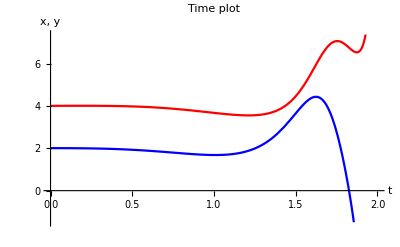

```mathematica
Plot[sol1,{t,0,2},PlotLabel->"Time plot",AxesLabel->{"t","x, y"},PlotStyle->{Blue,Red}]
```

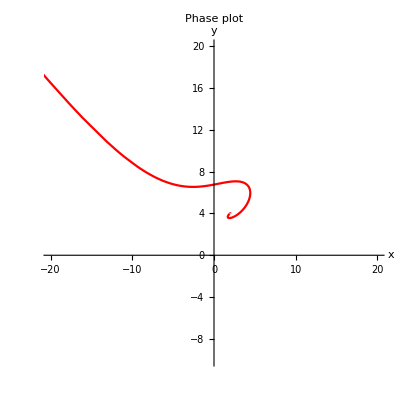

```mathematica
ParametricPlot[sol1,{t,0,2},PlotRange->{{-20,20},{-10,20}},PlotStyle->Red,AspectRatio->1,PlotLabel->"Phase plot", AxesLabel->{"x","y"}]
```

(e) Plot a phase portrait of the system for initial values {x,y}={2.01,4.01}, {0.01,0}, {-0.01,0}, {6,-10}, {7,-10}.

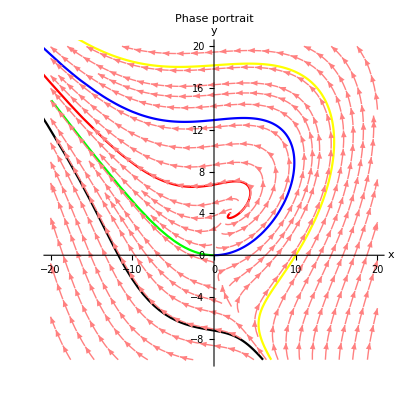

```mathematica
init2={x[0]==0.01,y[0]==0.0};
init3={x[0]==-0.01,y[0]==0.0};
init4={x[0]==6.,y[0]==-10.};
init5={x[0]==7.,y[0]==-10.};
sol2=NDSolveValue[{Df,Dg,init2},{x[t],y[t]},{t,0,1.1}];
sol3=NDSolveValue[{Df,Dg,init3},{x[t],y[t]},{t,0,0.9}];
sol4=NDSolveValue[{Df,Dg,init4},{x[t],y[t]},{t,0,0.4}];
sol5=NDSolveValue[{Df,Dg,init5},{x[t],y[t]},{t,0,0.4}];
p1=ParametricPlot[{sol1,sol2},{t,0,2},PlotRange->{{-20,20},{-10,20}},PlotStyle->{Red,Blue},AspectRatio->1,PlotLabel->"Phase portrait", AxesLabel->{"x","y"}];
p2=ParametricPlot[sol3,{t,0,.9},PlotRange->{{-20,20},{-10,20}},PlotStyle->{Green}];
p3=ParametricPlot[{sol4,sol5},{t,0,.4},PlotRange->{{-20,20},{-10,20}},PlotStyle->{Black,Yellow}];
Show[p1,p2,p3,StreamPlot [{f,g},{x,-20,20},{y,-10,20},StreamScale->{Tiny,Automatic,0.01}, StreamStyle->Pink]]
```

### 9-2: 2-species competition model

Consider the following system of differential equations describing competition between two species N_1 and N_2: (ⅆ N_1)/ⅆt=N_1(r_1-a_11 N_1-a_12 N_2), (ⅆ N_2)/ⅆt=N_2(r_2-a_21 N_1-a_22 N_2). For your analysis, use the specific values r_1=4, r_2=8, a_11=a_12=a_22=1, a_21=3.

(a) Calculate the four equilibria of the system.

```mathematica
f=N1*(4-N1-N2);
g=N2*(8-3*N1-N2);
equil=Values[NSolve[{f==0,g==0},{N1,N2}]];
MatrixForm[equil]
```

(0. | 8.
4. | 0.
2. | 2.
0. | 0.)

(b) Calculate the Jacobian for each equilibrium in (a)

```mathematica
jac=D[{f,g},{{N1,N2}}];
MatrixForm[jac]
```

(4-2 N1-N2 | -N1
-3 N2 | 8-3 N1-2 N2)

```mathematica
jac1=jac/.{N1->equil[[1,1]],N2->equil[[1,2]]};
MatrixForm[jac1]
jac2=jac/.{N1->equil[[2,1]],N2->equil[[2,2]]};
MatrixForm[jac2]
jac3=jac/.{N1->equil[[3,1]],N2->equil[[3,2]]};
MatrixForm[jac3]
jac4=jac/.{N1->equil[[4,1]],N2->equil[[4,2]]};
MatrixForm[jac4]
```

(-4. | 0.
-24. | -8.)

(-4. | -4.
0. | -4.)

(-2. | -2.
-6. | -2.)

(4. | 0.
0. | 8.)

(c) Which equilibria are stable and which are unstable? Do you expect oscillations?

```mathematica
Eigenvalues[jac1]
Det[jac1]
Tr[jac1]
```

{-8.,-4.}

32.

-12.

λ1 < 0, λ2 < 0: Scenario R1 (solutions converge towards zero = stable node)

```mathematica
Eigenvalues[jac2]
Det[jac2]
Tr[jac2]
```

{-4.,-4.}

16.

-8.

λ1 < 0, λ2 < 0: Scenario R1 (solutions converge towards zero = stable node)

```mathematica
Eigenvalues[jac3]
Det[jac3]
Tr[jac3]
```

```mathematica
{-5.464101615137755,1.4641016151377544}
```

{-5.4641,1.4641}

λ1 < 0, λ2 > 0: Scenario R3 (solutions diverge to infinity = saddle point)

```mathematica
Eigenvalues[jac4]
Det[jac4]
Tr[jac4]
```

{8.,4.}

32.

12.

λ1 > 0, λ2 > 0: Scenario R2 (solutions diverge to infinity = unstable node)

(d) Solve the system numerically for initial values {N1(0),N2(0)}={1.99,2.01} and plot the solutions in a time plot and a phase plot.

```mathematica
Df=D[N1[t],t]==N1[t]*(4-N1[t]-N2[t]);
Dg=D[N2[t],t]==N2[t]*(8-3*N1[t]-N2[t]);
init1={N1[0]==1.99,N2[0]==2.01};
sol1=NDSolveValue[{Df,Dg,init1},{N1[t],N2[t]},{t,0,20}];
```

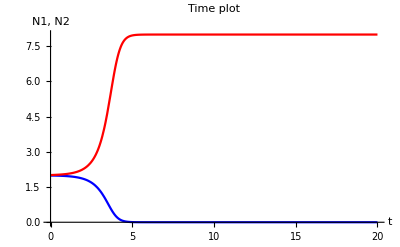

```mathematica
Plot[sol1,{t,0,20},PlotLabel->"Time plot",AxesLabel->{"t","N1, N2"},PlotStyle->{Blue,Red}]
```

```mathematica
ParametricPlot[sol1,{t,0,20},PlotRange->{{0,5},{0,10}},PlotStyle->Red,AspectRatio->1,PlotLabel->"Phase plot", AxesLabel->{"N1","N2"}];
```

{InterpolatingFunction[{{0., 20.}}, <>][t],InterpolatingFunction[{{0., 20.}}, <>][t]}

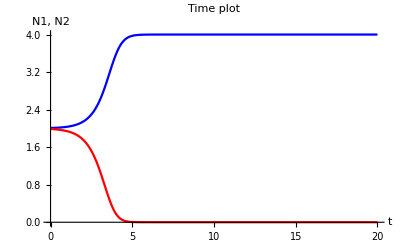

```mathematica
init2={N1[0]==2.01,N2[0]==1.99};
sol2=NDSolveValue[{Df,Dg,init2},{N1[t],N2[t]},{t,0,20}]
Plot[sol2,{t,0,20},PlotLabel->"Time plot",AxesLabel->{"t","N1, N2"},PlotStyle->{Blue,Red}]
ParametricPlot[sol2,{t,0,20},PlotRange->{{0,5},{0,10}},PlotStyle->Red,AspectRatio->1,PlotLabel->"Phase plot", AxesLabel->{"N1","N2"}];
```

Stable coexistence is not possible; one species will out-compete the other depending on the initial conditions.

### 9-3: Host-parasite interactions: The Nicholson-Bailey model

The Nicholson-Bailey model can be described by the following system of recurrence equations: H_(t+1)=R·H_t e^-aP_t, P_(t+1)=c·H_t(1-e^-aP_t). Assume in your analysis that a=c=1.

(a) Show that the equilibrium of the system equals Ĥ=(Rln(R))/(R-1),  P̂=ln(R).

```mathematica
h= R*H*Exp[-P];
p=H*(1-Exp[-P]);
sol=Values[Solve[{h==H,p==P},{H,P}]]
Refine[sol,Assumptions->R>0&& R≠1]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is Log[ⅇ^H] == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{-(R Log[1/R])/(-1+R),-Log[1/R]}}

{{(R Log[R])/(-1+R),Log[R]}}

```mathematica
sol=Values[Solve[{h==H,p==P},{H,P},Reals]]
Refine[sol,Assumptions->R>0&& R≠1]
```

{{0,0},{ConditionalExpression[(R Log[R])/(-1+R),0<R<1||R>1],ConditionalExpression[Log[R],0<R<1||R>1]}}

{{0,0},{(R Log[R])/(-1+R),Log[R]}}

(b) Show that this equilibrium is always unstable.

```mathematica
jac=D[{h,p},{{H,P}}]
MatrixForm[jac]
```

{{ⅇ^-P R,-ⅇ^-P H R},{1-ⅇ^-P,ⅇ^-P H}}

(ⅇ^-P R | -ⅇ^-P H R
1-ⅇ^-P | ⅇ^-P H)

```mathematica
Eigenvalues[jac]/.{H->sol[[1,1]],P->sol[[1,2]]}
Det[jac]/.{H->sol[[1,1]],P->sol[[1,2]]}
Tr[jac]/.{H->sol[[1,1]],P->sol[[1,2]]}
```

{1/2 (R-√(R^2)),1/2 (R+√(R^2))}

0

R

```mathematica
SymbolName[R]
```

R

```mathematica
Eigenvalues[jac]/.{H->sol[[2,1]],P->sol[[2,2]]}
Det[jac]/.{H->sol[[2,1]],P->sol[[2,2]]}
Tr[jac]/.{H->sol[[2,1]],P->sol[[2,2]]}
```

{ConditionalExpression[(R+(R Log[R])/(-1+R)-√(R^2+(2 R^2 Log[R])/(-1+R)-(4 R^3 Log[R])/(-1+R)+(R^2 Log[R]^2)/(-1+R)^2))/(2 R),0<R<1||R>1],ConditionalExpression[(R+(R Log[R])/(-1+R)+√(R^2+(2 R^2 Log[R])/(-1+R)-(4 R^3 Log[R])/(-1+R)+(R^2 Log[R]^2)/(-1+R)^2))/(2 R),0<R<1||R>1]}

ConditionalExpression[(R Log[R])/(-1+R),0<R<1||R>1]

ConditionalExpression[1+Log[R]/(-1+R),0<R<1||R>1]

(c) Use the density-dependent Nicholson-Bailey model: H_(t+1)=R·H_t e^(-bH_t-aP_t), P_(t+1)=c·H_t(1-e^-aP_t). Assume again that a=c=1. For parameter values b=0.5 and R=4, and initial values H_0=2.0 and P_0=1.0, plot the system and calculate the new equilibrium. Is the system stable and/or oscillating? Hint: Program a function in Mathematica using the command Manipulate[] to vary the values of R and b.

```mathematica
eq1= H[t+1]==R*H[t]*Exp[-b*H[t]-P[t]];
eq2=P[t+1]==H[t]*(1-Exp[-P[t]]);
init={H[0]==2.0,P[0]==1.0};
param1={b->0.5,R->4};
RSolveValue[{eq1,eq2,init},{H[t],P[t]},t]/.param1
```

RSolveValue[{H[1+t]==4 ⅇ^(-0.5 H[t]-P[t]) H[t],P[1+t]==(1-ⅇ^(-P[t])) H[t],{H[0]==2.,P[0]==1.}},{H[t],P[t]},t]

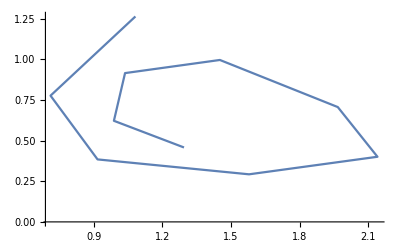

```mathematica
pts1=RecurrenceTable[{eq1,eq2,init},{H[t],P[t]},{t,1,10}]/.param1;
ListLinePlot[pts1,PlotRange->All]
```

(d) Do the same for parameter values b=0.25 and R=5. Is the system stable and/or oscillating?

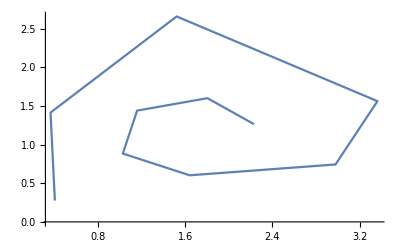

```mathematica
param2={b->0.25,R->5};
pts2=RecurrenceTable[{eq1,eq2,init},{H[t],P[t]},{t,1,10}]/.param2;
ListLinePlot[pts2,PlotRange->All]
```

```mathematica
plotNicholsonBailey[p1_,p2_]:=Module[{eq1,eq2,init,t,pts},
eq1= H[t+1]==p1*H[t]*Exp[-p2*H[t]-P[t]];
eq2=P[t+1]==H[t]*(1-Exp[-P[t]]);
init={H[0]==2.0,P[0]==1.0};
pts=RecurrenceTable[{eq1,eq2,init},{H[t],P[t]},{t,1,10}];
ListLinePlot[pts,PlotRange->All]
]
```

```mathematica
Manipulate[plotNicholsonBailey[R,b],{R,3,6},{b,0.1,0.9}]
```